```mathematica
f1[c_, s_, i_] := (c - a) (1 - c) - α s - β i;
```

```mathematica
f2[c_, s_, i_] := rs (1 - s) - γ c + δ i;
```

```mathematica
f3[c_, s_, i_] := ri ( 1 - i ) + η c;
```

```mathematica
solc[i_] := First[c /. Solve[f3[c, s, i] == 0, c]];
```

```mathematica
params = List[
ri1 =0.595, 
rs1=0.6, 
γ1=0.054, 
δ1=0.012, 
α1=0.33,
β1= 0.06,
a1 =2.83,
η1=0.365 ];
```

## Steady states distinct to (0, 0, 0)

```mathematica
F1[s_, i_] := Simplify[f1[solc[i], s, i]]
```

```mathematica
F2[s_, i_] := Simplify[ f2[solc[i], s, i]];
```

```mathematica
F1all[s_, i_, α_, β_, η_, a_, ri_]= F1[s,i];
```

```mathematica
F2all[s_, i_, δ_, γ_, η_, ri_, rs_] = F2[s,i];
```

```mathematica
F2[s,i]
```

rs-rs s+i δ-((-1+i) ri γ)/η

```mathematica
F1all[s, i, α, β, η, a, ri]
```

-s α-i β+(((-1+i) ri-η) (ri-i ri+a η))/η^2

## The nullclines are intersections of F1all and F2all, we can see the vector field to describe dynamic around steady states

```mathematica
Manipulate[
 Show[
  {VectorPlot[
    {F1all[s, i, α, β, η, a, ri],
     F2all[s, i, δ, γ, η, ri, rs] },
     {s, -1,5}, 
    {i, -1, 5},
    LabelStyle -> Directive[Black, FontFamily -> "Helvetica", FontSize -> 18],
    Axes -> True,
    Frame -> False,
     AxesLabel -> {Style["s", 45, Gray], Style["i", 45, Gray]},
  VectorPoints -> Coarse],   
   ContourPlot[
    {F1all[s, i, α, β, η, a, ri] == 0,
    F2all[s, i, δ, γ, η, ri, rs]  == 0},
     {s, -1,5}, 
    {i, -1, 5},
 PlotLegends ->{Style["f1", 25] , Style["f2" , 25]},
 ContourStyle -> {{Red,  Thickness[0.007]},{Blue, Thickness[0.007]} },
  LabelStyle -> Directive[Black, FontFamily -> "Helvetica", FontSize -> 14]
   ]
   }
  ] ,
{{ri , params[[1]]}, 0, 1},
 {{rs , params[[2]]}, 0, 1},
 {{γ, params[[3]]}, 0, 1},
 {{δ, params[[4]]}, 0, 1},
 {{α, params[[5]]}, 0, 10},
 {{β, params[[6]]}, 0, 5},
 {{a, params[[7]]}, 0, 10},
 {{η, params[[8]]}, 0.01, 5}]
```

## Now we compute the explicit values to two steady states

```mathematica
ssteady1[i_] = Collect[ s /. Solve[ Simplify[ Expand[ F1[s, i] ]] == 0 , s][[1, 1]], i];
```

```mathematica
ssteady2[i_] = Collect[ s /. Solve[ Simplify[ Expand[ F2[s, i] ]] == 0 , s][[1, 1]], i];
```

```mathematica
Solve[ Simplify[ Expand[ F1[s, i] ]] == 0 , s]
```

{{s→-(a+i β+((-1+i)^2 ri^2)/η^2-((1+a) (-1+i) ri)/η)/α}}

```mathematica
sintersec = Solve[ Simplify[ Expand[ ssteady1[i] ]] == ssteady2[i] , i];
```

```mathematica
sintersec2 = i /. sintersec ;
```

```mathematica
isol1[ γ_, η_, β_, a_, α_, δ_, ri_, rs_]=Part[sintersec2, 1];
```

```mathematica
isol2[γ_, η_, β_, a_, α_, δ_, ri_, rs_] = Part[sintersec2, 2];
```

```mathematica
ssol1[ γ_, η_, β_, a_, α_, δ_, ri_, rs_]=FullSimplify [ssteady1[i] /. {i -> isol1[ γ, η, β, a, α, δ, ri, rs]}];
```

```mathematica
ssol2[ γ_, η_, β_, a_, α_, δ_, ri_, rs_]=FullSimplify [ssteady1[i] /. {i -> isol2[ γ, η, β, a, α, δ, ri, rs]}];
```

```mathematica
csol1[γ_, η_, β_, a_, α_, δ_, ri_, rs_] = FullSimplify [solc[i] /. {i -> isol1[ γ, η, β, a, α, δ, ri, rs]}];
```

```mathematica
csol2[γ_, η_, β_, a_, α_, δ_, ri_, rs_] = FullSimplify [solc[i] /. {i -> isol2[ γ, η, β, a, α, δ, ri, rs]}];
```

```mathematica
Manipulate[
 { solution1 = {
 csol1[γ, η, β, a, α, δ, ri, rs] ,
 ssol1[ γ, η, β, a, α, δ, ri, rs],
 isol1[ γ, η, β, a, α, δ, ri, rs]}},
{{ri , params[[1]]}, 0, 1},
 {{rs , params[[2]]}, 0, 1},
 {{γ, params[[3]]}, 0, 1},
 {{δ, params[[4]]}, 0, 1},
 {{α, params[[5]]}, 0, 10},
 {{β, params[[6]]}, 0, 5},
 {{a, params[[7]]}, 0, 10},
 {{η, params[[8]]}, 0.01, 5}]
```

```mathematica
Manipulate[
 { solution2 ={
csol2[γ, η, β, a, α, δ, ri, rs],
 ssol2[ γ, η, β, a, α, δ, ri, rs],
 isol2[ γ, η, β, a, α, δ, ri, rs]}
 },
{{ri , params[[1]]}, 0, 1},
 {{rs , params[[2]]}, 0, 1},
 {{γ, params[[3]]}, 0, 1},
 {{δ, params[[4]]}, 0, 1},
 {{α, params[[5]]}, 0, 10},
 {{β, params[[6]]}, 0, 5},
 {{a, params[[7]]}, 0, 10},
 {{η, params[[8]]}, 0.01, 5}]
```

```mathematica
f1eval[c_, s_, i_,a_, α_, β_] := c((c - a) (1 - c) - α s - β i);
```

```mathematica
f2eval[c_, s_, i_,rs_,γ_,δ_] := s(rs (1 - s) - γ c + δ i);
```

```mathematica
f3eval[c_, s_, i_,ri_, η_ ] := i(ri ( 1 - i ) + η c);
```

#### First solution

```mathematica
f1eval[solution1[[1]], 
solution1[[2]], 
solution1[[3]],
params[[7]], 
params[[5]], 
params[[6]]]
```

7.09696×10^-16

```mathematica
f2eval[solution1[[1]], 
solution1[[2]], 
solution1[[3]],
params[[2]], 
params[[3]], 
params[[4]]]
```

8.83273×10^-17

```mathematica
f3eval[solution1[[1]], 
solution1[[2]], 
solution1[[3]],
params[[1]], 
params[[8]]]
```

0.

#### Second solution

```mathematica
f1eval[solution2[[1]], 
solution2[[2]], 
solution2[[3]],
params[[7]], 
params[[5]], 
params[[6]]]
```

-3.50246×10^-16

```mathematica
f2eval[solution2[[1]], 
solution2[[2]], 
solution2[[3]],
params[[2]], 
params[[3]], 
params[[4]]]
```

9.59557×10^-17

```mathematica
f3eval[solution2[[1]], 
solution2[[2]], 
solution2[[3]],
params[[1]], 
params[[8]]]
```

9.84825×10^-17

#### Rare solution

```mathematica
f1eval[0, 
1, 
1,
params[[7]], 
params[[5]], 
params[[6]]]
```

0.

```mathematica
f2eval[0, 
1, 
1,
params[[2]], 
params[[3]], 
params[[4]]]
```

0.012

```mathematica
f3eval[0, 
1, 
1,
params[[1]], 
params[[8]]]
```

0.

## Numeric solutions to differential equations

```mathematica
tf = 100
```

100

## fist steady state with P0=(2.556,0.821,2.568)

```mathematica
g1 = NDSolve[{
      c'[t] == c[t] ( (c[t] - a) (1 - c[t]) - α  s[t] - β  i[t]),
      s'[t] == s[t] (rs (1 - s[t]) - γ c[t] + δ i[t]),
     i'[t] ==i[t] ( ri ( 1 - i[t] ) + η c[t]),
        c[0] == solution1[[1]], 
   s[0] == solution1[[2]], 
       i[0] ==solution1[[3]]} /. {
         ri -> params[[1]],
       rs ->  params[[2]],
       γ -> params[[3]],
       δ -> params[[4]],
       α ->  params[[5]],
       β ->  params[[6]],
       a -> params[[7]],
       η ->params[[8]]},
     {c, s, i}, 
  {t, 0, tf},
  MaxSteps -> ∞];
```

```mathematica
solEdo1 = {c, s, i} /. g1[[1]];
```

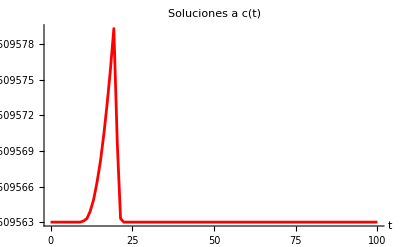

```mathematica
Plot[
c[t]/. g1, {t, 0, tf}, 
LabelStyle -> Directive[Black, FontFamily -> "Helvetica", FontSize -> 12],
PlotStyle -> Directive[Red, Thickness[0.005]],
AxesLabel -> {Style["t", 20, Gray]},
PlotRange->All,
PlotLabel ->Style[ "Soluciones a c(t)", 20, Gray],
ImageSize -> Scaled[0.3]]
```

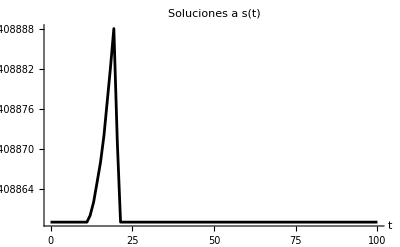

```mathematica
Plot[s[t]/. g1, {t, 0, tf}, 
LabelStyle -> Directive[Black, FontFamily -> "Helvetica", FontSize -> 12],
PlotStyle -> Directive[Black, Thickness[0.005]],
AxesLabel -> {Style["t", 20, Gray]},
PlotRange->All,
PlotLabel ->Style[ "Soluciones a s(t)", 20, Gray],
ImageSize -> Scaled[0.3]]
```

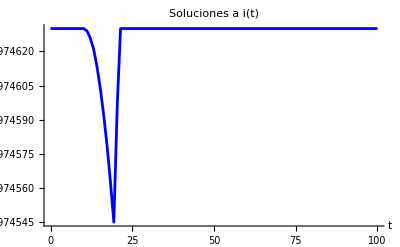

```mathematica
Plot[i[t]/. g1, {t, 0, tf}, 
LabelStyle -> Directive[Black, FontFamily -> "Helvetica", FontSize -> 12],
PlotStyle -> Directive[Blue, Thickness[0.005]],
AxesLabel -> {Style["t", 20, Gray]},
PlotRange->All,
PlotLabel ->Style[ "Soluciones a i(t)", 20, Gray],
ImageSize -> Scaled[0.3]]
```

## Second steady state with P0=(1.26189,0.921912,1.7741)

```mathematica
g2 =  NDSolve[{
      c'[t] == c[t] ( (c[t] - a) (1 - c[t]) - α  s[t] - β  i[t]),
      s'[t] == s[t] (rs (1 - s[t]) - γ c[t] + δ i[t]),
     i'[t] ==i[t] ( ri ( 1 - i[t] ) + η c[t]),
        c[0] == solution2[[1]], 
   s[0] == solution2[[2]], 
       i[0] ==solution2[[3]]} /. {
         ri -> params[[1]],
       rs ->  params[[2]],
       γ -> params[[3]],
       δ -> params[[4]],
       α ->  params[[5]],
       β ->  params[[6]],
       a -> params[[7]],
       η ->params[[8]]},
     {c, s, i}, 
  {t, 0, tf},
  MaxSteps -> ∞];
```

```mathematica
solEdo2 = {c, s, i} /. g2[[1]];
```

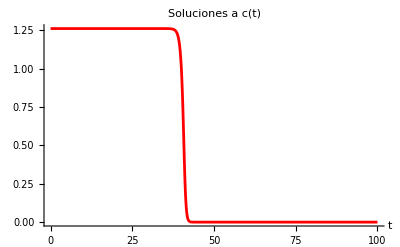

```mathematica
Plot[
c[t]/. g2, {t, 0, tf},  
LabelStyle -> Directive[Black, FontFamily -> "Helvetica", FontSize -> 12],
PlotStyle -> Directive[Red, Thickness[0.005]],
AxesLabel -> {Style["t", 20, Gray]},
PlotRange->All,
PlotLabel ->Style[ "Soluciones a c(t)", 20, Gray],
ImageSize -> Scaled[0.3]]
```

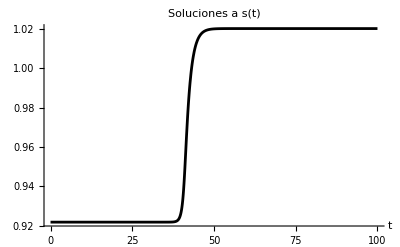

```mathematica
Plot[
s[t]/. g2, {t, 0, tf},  
LabelStyle -> Directive[Black, FontFamily -> "Helvetica", FontSize -> 12],
PlotStyle -> Directive[Black, Thickness[0.005]],
AxesLabel -> {Style["t", 20, Gray]},
PlotRange->All,
PlotLabel ->Style[ "Soluciones a s(t)", 20, Gray],
ImageSize -> Scaled[0.3]]
```

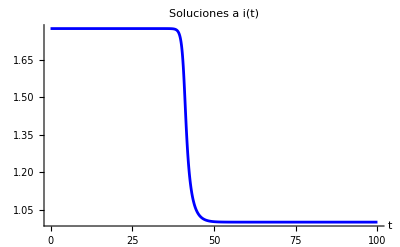

```mathematica
Plot[
i[t]/. g2, {t, 0, tf},  
LabelStyle -> Directive[Black, FontFamily -> "Helvetica", FontSize -> 12],
PlotStyle -> Directive[Blue, Thickness[0.005]],
AxesLabel -> {Style["t", 20, Gray]},
PlotRange->All,
PlotLabel ->Style[ "Soluciones a i(t)", 20, Gray],
ImageSize -> Scaled[0.3]]
```

## Third steady state with P0=(0,0,0)

```mathematica
g3 =  NDSolve[{
      c'[t] == c[t] ( (c[t] - a) (1 - c[t]) - α  s[t] - β  i[t]),
      s'[t] == s[t] (rs (1 - s[t]) - γ c[t] + δ i[t]),
     i'[t] ==i[t] ( ri ( 1 - i[t] ) + η c[t]),
        c[0] == 0, 
   s[0] == 0, 
       i[0] ==0} /. {
         ri -> params[[1]],
       rs ->  params[[2]],
       γ -> params[[3]],
       δ -> params[[4]],
       α ->  params[[5]],
       β ->  params[[6]],
       a -> params[[7]],
       η ->params[[8]]},
     {c, s, i}, 
  {t, 0, tf},
  MaxSteps -> ∞];
```

```mathematica
solEdo3 = {c, s, i} /. g3[[1]];
```

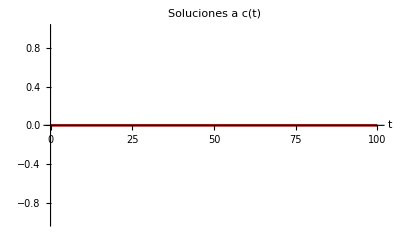

```mathematica
Plot[
c[t]/. g3, {t, 0, tf}, 
LabelStyle -> Directive[Black, FontFamily -> "Helvetica", FontSize -> 12],
PlotStyle -> Directive[Red, Thickness[0.005]],
AxesLabel -> {Style["t", 20, Gray]},
PlotLabel ->Style[ "Soluciones a c(t)", 20, Gray],
ImageSize -> Scaled[0.3]]
```

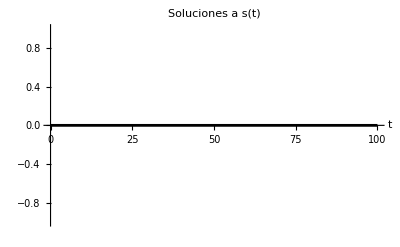

```mathematica
Plot[
s[t]/. g3, {t, 0, tf}, 
LabelStyle -> Directive[Black, FontFamily -> "Helvetica", FontSize -> 12],
PlotStyle -> Directive[Black, Thickness[0.005]],
AxesLabel -> {Style["t", 20, Gray]},
PlotLabel ->Style[ "Soluciones a s(t)", 20, Gray],
ImageSize -> Scaled[0.3]]
```

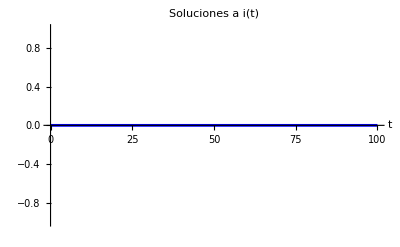

```mathematica
Plot[
i[t]/. g3, {t, 0, tf}, 
LabelStyle -> Directive[Black, FontFamily -> "Helvetica", FontSize -> 12],
PlotStyle -> Directive[Blue, Thickness[0.005]],
AxesLabel -> {Style["t", 20, Gray]},
PlotLabel ->Style[ "Soluciones a i(t)", 20, Gray],
ImageSize -> Scaled[0.3]]
```

```mathematica
Known steady state with P0=(0,1,1)
```

Known steady state with P0=(0,1,1)

```mathematica
g4 =  NDSolve[{
      c'[t] == c[t] ( (c[t] - a) (1 - c[t]) - α  s[t] - β  i[t]),
      s'[t] == s[t] (rs (1 - s[t]) - γ c[t] + δ i[t]),
     i'[t] ==i[t] ( ri ( 1 - i[t] ) + η c[t]),
        c[0] == 0, 
   s[0] == 1, 
       i[0] ==1} /. {
         ri -> params[[1]],
       rs ->  params[[2]],
       γ -> params[[3]],
       δ -> params[[4]],
       α ->  params[[5]],
       β ->  params[[6]],
       a -> params[[7]],
       η ->params[[8]]},
     {c, s, i}, 
  {t, 0, tf},
  MaxSteps -> ∞];
```

```mathematica
Plot[
c[t]/. g4, {t, 0, tf}, 
LabelStyle -> Directive[Black, FontFamily -> "Helvetica", FontSize -> 12],
PlotStyle -> Directive[Red, Thickness[0.005]],
AxesLabel -> {Style["t", 20, Gray]},
PlotLabel ->Style[ "Soluciones a c(t)", 20, Gray],
ImageSize -> Scaled[0.3]]
```

-Graphics-

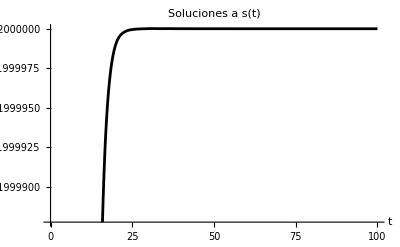

```mathematica
Plot[
s[t]/. g4, {t, 0, tf}, 
LabelStyle -> Directive[Black, FontFamily -> "Helvetica", FontSize -> 12],
PlotStyle -> Directive[Black, Thickness[0.005]],
AxesLabel -> {Style["t", 20, Gray]},
PlotLabel ->Style[ "Soluciones a s(t)", 20, Gray],
ImageSize -> Scaled[0.3]]
```

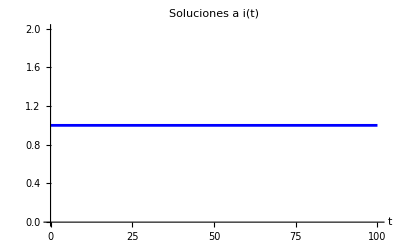

```mathematica
Plot[
i[t]/. g4, {t, 0, tf}, 
LabelStyle -> Directive[Black, FontFamily -> "Helvetica", FontSize -> 12],
PlotStyle -> Directive[Blue, Thickness[0.005]],
AxesLabel -> {Style["t", 20, Gray]},
PlotLabel ->Style[ "Soluciones a i(t)", 20, Gray],
ImageSize -> Scaled[0.3]]
```

```mathematica
l = {c[t], s[t], i[t]};
```

```mathematica
ParametricPlot3D[
Evaluate[l /. g3],
 {t, 0, tf},
 PlotPoints -> 100,
 PlotRange -> All,
 AxesLabel -> {"Cancer", "Sanas", "Inmunes"},
BoxRatios -> {1, 1, 1},
 PlotStyle -> Directive[Thick, RGBColor[.8, 0, 0]],
 ColorFunction -> (ColorData["SolarColors", #4] &)]
```

-Graphics3D-

## Linear analisys stability

```mathematica
cDotLap[s_, c_, i_] = -Dc q^2 c + cDot[s, c, i];
```

```mathematica
sDotLap[s_, c_, i_] =  -Ds q^2 s + sDot[s, c, i];
```

```mathematica
iDotLap[s_, c_, i_] =  -Di q^2 i + iDot[s, c, i] ;
```

```mathematica
Collect[
 Expand[ 
  Normal[ 
    Series[
     cDot[s + δs, c + δc, i + δi],
     {δs, 0, 1}, {δc, 0, 1}, {δi, 0, 1}
     ] 
    ] - cDot[s, c, i]
  ],
 {δs, δc, δi}
 ]
```

δi cDot^(0,0,1)[s,c,i]+δc (cDot^(0,1,0)[s,c,i]+δi cDot^(0,1,1)[s,c,i])+δs (cDot^(1,0,0)[s,c,i]+δi cDot^(1,0,1)[s,c,i]+δc (cDot^(1,1,0)[s,c,i]+δi cDot^(1,1,1)[s,c,i]))

```mathematica
Collect[
 Expand[ 
  Normal[ 
    Series[
     sDot[s + δs, c + δc, i + δi],
     {δs, 0, 1}, {δc, 0, 1}, {δi, 0, 1}
     ]
    ] - sDot[s, c, i]
  ],
 {δs, δc, δi}
 ]
```

δi sDot^(0,0,1)[s,c,i]+δc (sDot^(0,1,0)[s,c,i]+δi sDot^(0,1,1)[s,c,i])+δs (sDot^(1,0,0)[s,c,i]+δi sDot^(1,0,1)[s,c,i]+δc (sDot^(1,1,0)[s,c,i]+δi sDot^(1,1,1)[s,c,i]))

```mathematica
Collect[
 Expand[ 
  Normal[ 
    Series[
     iDot[s + δs, c + δc, i + δi],
     {δs, 0, 1}, {δc, 0, 1}, {δi, 0, 1}
     ]
    ] - iDot[s, c, i]
  ],
 {δs, δc, δi}
 ]
```

δi iDot^(0,0,1)[s,c,i]+δc (iDot^(0,1,0)[s,c,i]+δi iDot^(0,1,1)[s,c,i])+δs (iDot^(1,0,0)[s,c,i]+δi iDot^(1,0,1)[s,c,i]+δc (iDot^(1,1,0)[s,c,i]+δi iDot^(1,1,1)[s,c,i]))

```mathematica
DynamicMatrix = {
  {-Ds q^2 + rs - 2 rs s - c γ, -s γ, s δ },
  {-c α, 
   2 c + 2 a c + 3 c^2 - Dc q^2 - s α - 
    i β, -c β  },
  {0, i η, -Di q^2 + ri - 2 i ri + c η}
  }
```

{{-Ds q^2+rs-2 rs s-c γ,-s γ,s δ},{-c α,2 c+2 a c+3 c^2-Dc q^2-s α-i β,-c β},{0,i η,-Di q^2+ri-2 i ri+c η}}

```mathematica
lambda1[q_, s_, c_, i_, Ds_, Dc_, Di_, rs_,ri_, γ_, δ_, α_, a_, β_, η_] = Eigenvalues[DynamicMatrix][[1]];
```

```mathematica
lambda2[q_, s_, c_, i_, Ds_, Dc_, Di_, rs_, ri_, γ_, δ_, α_, a_, β_, η_] = Eigenvalues[DynamicMatrix][[2]];
```

```mathematica
lambda3[q_, s_, c_, i_, Ds_, Dc_, Di_, rs_, ri_, γ_, δ_, α_, a_, β_, η_] = Eigenvalues[DynamicMatrix][[3]];
```

```mathematica
lambda3[q, s, c, i, Ds, Dc, Di, rs,ri, γ, δ, α, a, β, η]
```

Root[-2 c Di Ds q^4-2 a c Di Ds q^4-3 c^2 Di Ds q^4+Dc Di Ds q^6+2 c Ds q^2 ri+2 a c Ds q^2 ri+3 c^2 Ds q^2 ri-4 c Ds i q^2 ri-4 a c Ds i q^2 ri-6 c^2 Ds i q^2 ri-Dc Ds q^4 ri+2 Dc Ds i q^4 ri+2 c Di q^2 rs+2 a c Di q^2 rs+3 c^2 Di q^2 rs-Dc Di q^4 rs-2 c ri rs-2 a c ri rs-3 c^2 ri rs+4 c i ri rs+4 a c i ri rs+6 c^2 i ri rs+Dc q^2 ri rs-2 Dc i q^2 ri rs-4 c Di q^2 rs s-4 a c Di q^2 rs s-6 c^2 Di q^2 rs s+2 Dc Di q^4 rs s+4 c ri rs s+4 a c ri rs s+6 c^2 ri rs s-8 c i ri rs s-8 a c i ri rs s-12 c^2 i ri rs s-2 Dc q^2 ri rs s+4 Dc i q^2 ri rs s+Di Ds q^4 s α-Ds q^2 ri s α+2 Ds i q^2 ri s α-Di q^2 rs s α+ri rs s α-2 i ri rs s α+2 Di q^2 rs s^2 α-2 ri rs s^2 α+4 i ri rs s^2 α+Di Ds i q^4 β-Ds i q^2 ri β+2 Ds i^2 q^2 ri β-Di i q^2 rs β+i ri rs β-2 i^2 ri rs β+2 Di i q^2 rs s β-2 i ri rs s β+4 i^2 ri rs s β-2 c^2 Di q^2 γ-2 a c^2 Di q^2 γ-3 c^3 Di q^2 γ+c Dc Di q^4 γ+2 c^2 ri γ+2 a c^2 ri γ+3 c^3 ri γ-4 c^2 i ri γ-4 a c^2 i ri γ-6 c^3 i ri γ-c Dc q^2 ri γ+2 c Dc i q^2 ri γ+c Di i q^2 β γ-c i ri β γ+2 c i^2 ri β γ+2 c^2 Ds q^2 η+2 a c^2 Ds q^2 η+3 c^3 Ds q^2 η-c Dc Ds q^4 η-2 c^2 rs η-2 a c^2 rs η-3 c^3 rs η+c Dc q^2 rs η+4 c^2 rs s η+4 a c^2 rs s η+6 c^3 rs s η-2 c Dc q^2 rs s η-c Ds q^2 s α η+c rs s α η-2 c rs s^2 α η+2 c^3 γ η+2 a c^3 γ η+3 c^4 γ η-c^2 Dc q^2 γ η+c i s α δ η+(-2 c Di q^2-2 a c Di q^2-3 c^2 Di q^2-2 c Ds q^2-2 a c Ds q^2-3 c^2 Ds q^2+Dc Di q^4+Dc Ds q^4+Di Ds q^4+2 c ri+2 a c ri+3 c^2 ri-4 c i ri-4 a c i ri-6 c^2 i ri-Dc q^2 ri-Ds q^2 ri+2 Dc i q^2 ri+2 Ds i q^2 ri+2 c rs+2 a c rs+3 c^2 rs-Dc q^2 rs-Di q^2 rs+ri rs-2 i ri rs-4 c rs s-4 a c rs s-6 c^2 rs s+2 Dc q^2 rs s+2 Di q^2 rs s-2 ri rs s+4 i ri rs s+Di q^2 s α+Ds q^2 s α-ri s α+2 i ri s α-rs s α+2 rs s^2 α+Di i q^2 β+Ds i q^2 β-i ri β+2 i^2 ri β-i rs β+2 i rs s β-2 c^2 γ-2 a c^2 γ-3 c^3 γ+c Dc q^2 γ+c Di q^2 γ-c ri γ+2 c i ri γ+c i β γ+2 c^2 η+2 a c^2 η+3 c^3 η-c Dc q^2 η-c Ds q^2 η+c rs η-2 c rs s η-c s α η-c^2 γ η) #1+(-2 c-2 a c-3 c^2+Dc q^2+Di q^2+Ds q^2-ri+2 i ri-rs+2 rs s+s α+i β+c γ-c η) #1^2+#1^3&,3]

```mathematica
Manipulate[
 Plot[  
  {Re[lambda1[q, s, c, i, Ds, Dc, Di, rs,ri, γ, δ, α, a, β, η]],
   Im[lambda1[q, s, c, i, Ds, Dc, Di, rs,ri, γ, δ, α, a, β, η]],
   Re[lambda2[q, s, c, i, Ds, Dc, Di, ri, γ, δ, α, a, β, η]],
   Im[lambda2[q, s, c, i, Ds, Dc, Di, rs,ri, γ, δ, α, a, β, η]],
   Re[lambda3[q, s, c, i, Ds, Dc, Di, rs,ri, γ, δ, α, a, β, η]],
   Im[lambda3[q, s, c, i, Ds, Dc, Di, rs,ri, γ, δ, α, a, β, η]]
   } , 
  {q, 0, 10},
  PlotRange -> {{0, 5}, {-1,1}}, 
  PlotStyle -> {Red, {Red, Dashed}, Black, {Black, Dashed}, Blue, {Blue, Dashed}}, 
  Frame -> True,
  FrameLabel -> {"q", "λ"}, 
  PlotLegends -> {lambda1, lambda2, lambda3}],
 {{c ,  0}, 0, 3},
 {{s ,  0}, 0, 3},
 {{i,  0}, 0, 3},
 {{Ds , 1}, 0, 1},
 {{Dc , 1}, 0, 1},
 {{Di, 1}, 0, 1},
{{ri , params[[1]]}, 0, 1},
 {{rs , params[[2]]}, 0, 1},
 {{γ, params[[3]]}, 0, 1},
 {{δ, params[[4]]}, 0, 1},
 {{α, params[[5]]}, 0, 10},
 {{β, params[[6]]}, 0, 5},
 {{a, params[[7]]}, 0, 10},
 {{η, params[[8]]}, 0.01, 5}]
```

## Plot the vector field of dynamics

```mathematica
cDot[s_, c_, i_] := c*f1[c, s, i];
```

```mathematica
sDot[s_, c_, i_] := s*f2[c, s, i];
```

```mathematica
iDot[s_, c_, i_] := i*f3[c, s, i];
```

```mathematica
cDot2[s_, c_, i_,  β_, a_, α_] =   cDot[s, c, i];
```

```mathematica
sDot2[s_, c_, i_,rs_,  γ_,  δ_] = sDot[s, c, i];
```

```mathematica
iDot2[s_, c_, i_,ri_,η_]= iDot[s, c, i];
```

```mathematica
Manipulate[
 Show[StreamPlot3D[{
  cDot2[s, c, i, β, a, α],
   sDot2[s, c, i,rs,  γ,  δ] ,
   iDot2[s, c, i,ri,η]},
 {c, 2.4, 2.7},
  {s, 0.6, 1},
 {i, 2.2, 2.7},
 StreamMarkers -> "Arrow3D",
 PlotLegends -> Automatic,
 StreamPoints -> 80,
 AxesLabel -> {Style["s", Bold, 28],Style["i", Bold, 28],Style["c", Bold, 28]}],
  Graphics3D[{
Red, 
PointSize[0.05], 
Point[{
csol1[γ, η, β, a, α, δ, ri, rs],
ssol1[ γ, η, β, a, α, δ, ri, rs], 
isol1[ γ, η, β, a, α, δ, ri, rs]
}],
Point[{
csol2[γ, η, β, a, α, δ, ri, rs],
ssol2[ γ, η, β, a, α, δ, ri, rs], 
isol2[ γ, η, β, a, α, δ, ri, rs]
}],
Point[{0,0,0}],
}, 
Axes -> True]],
{{ri , params[[1]]}, 0, 1},
 {{rs , params[[2]]}, 0, 1},
 {{γ, params[[3]]}, 0, 1},
 {{δ, params[[4]]}, 0, 1},
 {{α, params[[5]]}, 0, 10},
 {{β, params[[6]]}, 0, 5},
 {{a, params[[7]]}, 0, 10},
 {{η, params[[8]]}, 0.01, 5}]
```